```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,30000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]
```

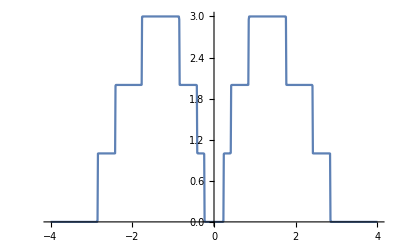

```mathematica
ListLinePlot[Table[{ω,Abs[tr[ω,0.0001,1,0]]},{ω,Range[-4,4,0.01]}]]
```

```mathematica
imp1[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{1,1}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp2[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{2,2}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp3[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{3,3}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp4[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{4,4}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp5[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{5,5}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp6[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{6,6}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp7[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{7,7}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp8[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{8,8}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp9[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{9,9}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp10[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{10,10}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp11[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{11,11}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp12[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{12,12}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp13[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{13,13}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp14[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{14,14}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{κ=β[ω,δ,t,ϵ]},ReplacePart[κ,{{14,14}}->ω+ⅈ*δ-0]]]
```

```mathematica
set1[ω_,δ_,t_,ϵ_,ϵ1_,num_,s_]:=RandomChoice[Join[RandomChoice[{imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp3[ω,δ,t,ϵ,ϵ1],imp4[ω,δ,t,ϵ,ϵ1],imp5[ω,δ,t,ϵ,ϵ1],imp6[ω,δ,t,ϵ,ϵ1],imp7[ω,δ,t,ϵ,ϵ1],imp8[ω,δ,t,ϵ,ϵ1],imp9[ω,δ,t,ϵ,ϵ1],imp10[ω,δ,t,ϵ,ϵ1],imp11[ω,δ,t,ϵ,ϵ1],imp12[ω,δ,t,ϵ,ϵ1],imp13[ω,δ,t,ϵ,ϵ1],imp14[ω,δ,t,ϵ,ϵ1]},num],Table[imp[ω,δ,t,ϵ,ϵ1],100-num]],100]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_,num_,s_]:=Module[{gg=g[ω,δ,t,ϵ],x=T1[1],T=TT[1]},
η=Module[{cc=RandomChoice[Join[RandomChoice[{imp1[ω,δ,t,ϵ,ϵ1],imp2[ω,δ,t,ϵ,ϵ1],imp3[ω,δ,t,ϵ,ϵ1],imp4[ω,δ,t,ϵ,ϵ1],imp5[ω,δ,t,ϵ,ϵ1],imp6[ω,δ,t,ϵ,ϵ1],imp7[ω,δ,t,ϵ,ϵ1],imp8[ω,δ,t,ϵ,ϵ1],imp9[ω,δ,t,ϵ,ϵ1],imp10[ω,δ,t,ϵ,ϵ1],imp11[ω,δ,t,ϵ,ϵ1],imp12[ω,δ,t,ϵ,ϵ1],imp13[ω,δ,t,ϵ,ϵ1],imp14[ω,δ,t,ϵ,ϵ1]},num],Table[imp[ω,δ,t,ϵ,ϵ1],100-num]],100]},
sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[14]-cc[[m]].ConjugateTranspose[x].J.x].cc[[m]],{m,1,s}]; J=J];
Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,δ,t,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,δ,1,0].T.sl1.T].SR[ω,δ,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,δ,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
η]
```

```mathematica
tr1[1.5,0.0001,1,0,0.40,100,14]
```

2.18031

```mathematica
Mean[Table[tr1[1.01,0.0001,1,0,0.7,100,100],10000]]
```

0.593137

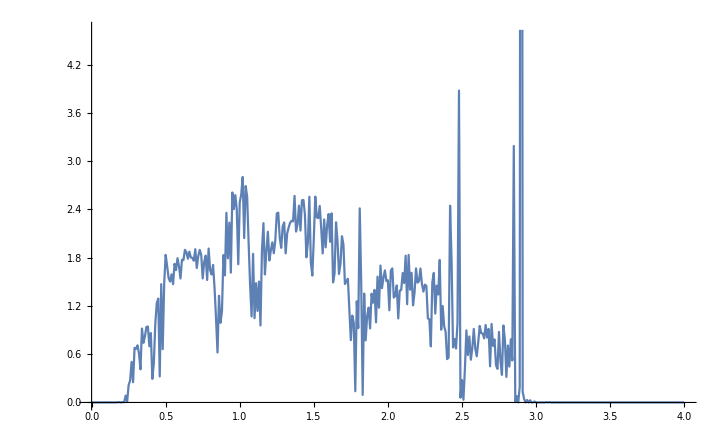

```mathematica
ListLinePlot[Table[{ω,tr1[ω,0.001,1,0,0.7,100,14]},{ω,Range[0,4,0.01]}]]
```

```mathematica
Timing[Mean[Table[tr1[1,0.0001,1,0,0.5],5000]]]
```

{35.896,0.939567}

```mathematica
Timing[Mean[Table[tr1[1,0.0001,1,0,0.5],5000]]]
```

{35.751,0.940068}

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.0001,1,0,0.5],5000]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.0000409657},{0.01,0.0000267908},{0.02,0.0000220225},{0.03,0.0000259849},{0.04,0.0000405016},{0.05,0.0000645224},{0.06,0.0000968583},{0.07,0.000143093},{0.08,0.00019961},{0.09,0.000267236},{0.1,0.000354365},{0.11,0.00047268},{0.12,0.000595619},{0.13,0.000755237},{0.14,0.000996938},{0.15,0.00124838},{0.16,0.00158664},{0.17,0.00208923},{0.18,0.00281468},{0.19,0.00364575},{0.2,0.0051286},{0.21,0.00719891},{0.22,0.0116664},{0.23,0.0224359},{0.24,0.0510574},{0.25,0.0633631},{0.26,0.0833811},{0.27,0.166198},{0.28,0.261679},{0.29,0.314104},{0.3,0.354589},{0.31,0.373892},{0.32,0.39298},{0.33,0.405694},{0.34,0.423753},{0.35,0.420064},{0.36,0.419912},{0.37,0.426916},{0.38,0.417462},{0.39,0.415225},{0.4,0.409333},{0.41,0.423488},{0.42,0.553748},{0.43,0.570837},{0.44,0.735296},{0.45,0.910762},{0.46,0.747969},{0.47,0.65022},{0.48,0.580818},{0.49,0.54836},{0.5,0.539617},{0.51,0.538594},{0.52,0.541474},{0.53,0.561596},{0.54,0.560642},{0.55,0.585676},{0.56,0.596693},{0.57,0.613834},{0.58,0.633955},{0.59,0.642635},{0.6,0.662817},{0.61,0.666735},{0.62,0.678429},{0.63,0.702838},{0.64,0.718635},{0.65,0.729832},{0.66,0.742382},{0.67,0.754273},{0.68,0.761561},{0.69,0.773661},{0.7,0.781532},{0.71,0.794243},{0.72,0.80689},{0.73,0.810437},{0.74,0.818609},{0.75,0.826433},{0.76,0.839526},{0.77,0.846062},{0.78,0.845025},{0.79,0.854925},{0.8,0.856125},{0.81,0.850324},{0.82,0.835544},{0.83,0.807152},{0.84,0.740221},{0.85,0.69421},{0.86,0.697686},{0.87,0.786114},{0.88,0.953967},{0.89,0.787219},{0.9,0.660414},{0.91,0.606245},{0.92,0.583098},{0.93,0.598001},{0.94,0.623337},{0.95,0.656351},{0.96,0.704941},{0.97,0.762818},{0.98,0.816025},{0.99,0.872394},{1.,0.935431},{1.01,1.05428},{1.02,0.964953},{1.03,0.720534},{1.04,0.441819},{1.05,0.348348},{1.06,0.355561},{1.07,0.375865},{1.08,0.364513},{1.09,0.345995},{1.1,0.332741},{1.11,0.331904},{1.12,0.335636},{1.13,0.340958},{1.14,0.35387},{1.15,0.364992},{1.16,0.379287},{1.17,0.395569},{1.18,0.40533},{1.19,0.417811},{1.2,0.431104},{1.21,0.439786},{1.22,0.450813},{1.23,0.462797},{1.24,0.477171},{1.25,0.472612},{1.26,0.484642},{1.27,0.490728},{1.28,0.479413},{1.29,0.486865},{1.3,0.491045},{1.31,0.49787},{1.32,0.485151},{1.33,0.499808},{1.34,0.493608},{1.35,0.496087},{1.36,0.50275},{1.37,0.492542},{1.38,0.493464},{1.39,0.493421},{1.4,0.492843},{1.41,0.487774},{1.42,0.48287},{1.43,0.489066},{1.44,0.477258},{1.45,0.466326},{1.46,0.476198},{1.47,0.471538},{1.48,0.459643},{1.49,0.453665},{1.5,0.445472},{1.51,0.445229},{1.52,0.435084},{1.53,0.430222},{1.54,0.421554},{1.55,0.421209},{1.56,0.413932},{1.57,0.411742},{1.58,0.409568},{1.59,0.408137},{1.6,0.401478},{1.61,0.406688},{1.62,0.399635},{1.63,0.402859},{1.64,0.399731},{1.65,0.415211},{1.66,0.423377},{1.67,0.452826},{1.68,0.477659},{1.69,0.515456},{1.7,0.59034},{1.71,0.664783},{1.72,0.773949},{1.73,0.921372},{1.74,1.21226},{1.75,1.68609},{1.76,2.78941},{1.77,7.27363},{1.78,6.3967},{1.79,5.34391},{1.8,3.48815},{1.81,2.07467},{1.82,1.06331},{1.83,0.560528},{1.84,0.35398},{1.85,0.330916},{1.86,0.336743},{1.87,0.362677},{1.88,0.383622},{1.89,0.405194},{1.9,0.417027},{1.91,0.425922},{1.92,0.447182},{1.93,0.452278},{1.94,0.465878},{1.95,0.479664},{1.96,0.473599},{1.97,0.469622},{1.98,0.463312},{1.99,0.473841},{2.,0.470165},{2.01,0.46777},{2.02,0.469434},{2.03,0.468307},{2.04,0.464246},{2.05,0.454459},{2.06,0.453062},{2.07,0.44744},{2.08,0.448027},{2.09,0.439854},{2.1,0.435001},{2.11,0.436679},{2.12,0.433113},{2.13,0.420591},{2.14,0.416424},{2.15,0.416993},{2.16,0.402637},{2.17,0.399555},{2.18,0.387871},{2.19,0.382489},{2.2,0.377301},{2.21,0.358102},{2.22,0.355923},{2.23,0.344055},{2.24,0.335997},{2.25,0.329068},{2.26,0.326148},{2.27,0.312677},{2.28,0.312672},{2.29,0.308999},{2.3,0.299023},{2.31,0.291451},{2.32,0.285558},{2.33,0.292138},{2.34,0.289289},{2.35,0.292368},{2.36,0.307287},{2.37,0.329862},{2.38,0.376224},{2.39,0.462992},{2.4,0.641354},{2.41,1.20756},{2.42,3.49316},{2.43,3.79914},{2.44,2.97516},{2.45,1.81428},{2.46,1.06363},{2.47,0.56934},{2.48,0.309319},{2.49,0.197599},{2.5,0.190599},{2.51,0.19047},{2.52,0.205456},{2.53,0.200009},{2.54,0.204374},{2.55,0.210785},{2.56,0.217868},{2.57,0.222927},{2.58,0.225643},{2.59,0.217607},{2.6,0.223807},{2.61,0.227986},{2.62,0.225718},{2.63,0.228917},{2.64,0.220236},{2.65,0.22118},{2.66,0.221613},{2.67,0.210057},{2.68,0.218536},{2.69,0.221396},{2.7,0.220393},{2.71,0.214158},{2.72,0.206361},{2.73,0.20288},{2.74,0.196325},{2.75,0.196267},{2.76,0.186313},{2.77,0.183102},{2.78,0.175492},{2.79,0.173496},{2.8,0.165689},{2.81,0.156147},{2.82,0.156082},{2.83,0.153091},{2.84,0.16567},{2.85,1.33545},{2.86,1.47617},{2.87,1.36951},{2.88,1.20014},{2.89,0.705323},{2.9,0.119125},{2.91,0.0219258},{2.92,0.00747174},{2.93,0.00483511},{2.94,0.00357084},{2.95,0.00265717},{2.96,0.00207796},{2.97,0.00174139},{2.98,0.00135422},{2.99,0.0011339},{3.,0.000952459},{3.01,0.00083183},{3.02,0.000738746},{3.03,0.00060898},{3.04,0.000545091},{3.05,0.000456689},{3.06,0.000401057},{3.07,0.000348208},{3.08,0.000300877},{3.09,0.00027591},{3.1,0.000247435},{3.11,0.000223208},{3.12,0.000202412},{3.13,0.000185268},{3.14,0.000161268},{3.15,0.000151386},{3.16,0.000135762},{3.17,0.000117706},{3.18,0.000106807},{3.19,0.000101315},{3.2,0.0000959425},{3.21,0.0000867615},{3.22,0.0000800772},{3.23,0.0000698155},{3.24,0.0000678285},{3.25,0.0000606977},{3.26,0.0000607876},{3.27,0.0000534324},{3.28,0.0000464665},{3.29,0.0000471328},{3.3,0.0000407002},{3.31,0.0000371714},{3.32,0.0000361348},{3.33,0.0000348237},{3.34,0.0000316631},{3.35,0.0000292921},{3.36,0.0000269262},{3.37,0.0000262912},{3.38,0.0000246441},{3.39,0.0000225822},{3.4,0.0000207927},{3.41,0.0000192281},{3.42,0.0000201357},{3.43,0.0000178863},{3.44,0.0000161196},{3.45,0.0000163639},{3.46,0.0000153577},{3.47,0.0000144138},{3.48,0.0000132799},{3.49,0.0000124865},{3.5,0.0000122247},{3.51,0.0000117065},{3.52,0.000010981},{3.53,0.0000101316},{3.54,9.4657×10^-6},{3.55,8.87995×10^-6},{3.56,8.37841×10^-6},{3.57,8.09721×10^-6},{3.58,7.44267×10^-6},{3.59,7.45789×10^-6},{3.6,6.83122×10^-6},{3.61,6.47236×10^-6},{3.62,6.01132×10^-6},{3.63,5.7195×10^-6},{3.64,5.89151×10^-6},{3.65,5.20155×10^-6},{3.66,5.23191×10^-6},{3.67,4.86704×10^-6},{3.68,4.69151×10^-6},{3.69,4.35117×10^-6},{3.7,4.31312×10^-6},{3.71,3.93222×10^-6},{3.72,3.81782×10^-6},{3.73,3.7494×10^-6},{3.74,3.47152×10^-6},{3.75,3.29883×10^-6},{3.76,3.1636×10^-6},{3.77,2.96711×10^-6},{3.78,2.79047×10^-6},{3.79,2.80175×10^-6},{3.8,2.59511×10^-6},{3.81,2.58847×10^-6},{3.82,2.36808×10^-6},{3.83,2.35828×10^-6},{3.84,2.27221×10^-6},{3.85,2.10566×10^-6},{3.86,1.99504×10^-6},{3.87,1.86472×10^-6},{3.88,1.88759×10^-6},{3.89,1.8176×10^-6},{3.9,1.6486×10^-6},{3.91,1.67481×10^-6},{3.92,1.59994×10^-6},{3.93,1.51035×10^-6},{3.94,1.48797×10^-6},{3.95,1.41×10^-6},{3.96,1.40877×10^-6},{3.97,1.27936×10^-6},{3.98,1.27405×10^-6},{3.99,1.18344×10^-6},{4.,1.12708×10^-6}}

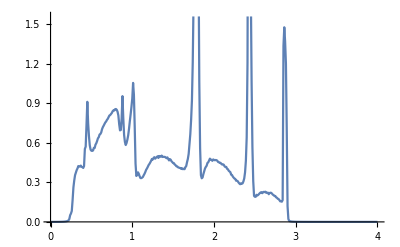

```mathematica
ListPlot[%142,Joined->True]
```

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.0001,1,0,0.7],5000]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000163151},{0.01,0.000127858},{0.02,0.0000920619},{0.03,0.0000830369},{0.04,0.0000988526},{0.05,0.000123534},{0.06,0.000175067},{0.07,0.000246918},{0.08,0.000344929},{0.09,0.000448178},{0.1,0.000585573},{0.11,0.000754577},{0.12,0.000959635},{0.13,0.0012683},{0.14,0.00160289},{0.15,0.0020554},{0.16,0.00259009},{0.17,0.00329267},{0.18,0.00436837},{0.19,0.00570373},{0.2,0.00777474},{0.21,0.0107904},{0.22,0.0166366},{0.23,0.0294629},{0.24,0.0609718},{0.25,0.0761839},{0.26,0.0915702},{0.27,0.124403},{0.28,0.154196},{0.29,0.176602},{0.3,0.194338},{0.31,0.221184},{0.32,0.236604},{0.33,0.240767},{0.34,0.254363},{0.35,0.262492},{0.36,0.260693},{0.37,0.275408},{0.38,0.289509},{0.39,0.296784},{0.4,0.323104},{0.41,0.430555},{0.42,0.643466},{0.43,0.630659},{0.44,0.686747},{0.45,0.823981},{0.46,0.861174},{0.47,0.773263},{0.48,0.66679},{0.49,0.608411},{0.5,0.545028},{0.51,0.493152},{0.52,0.467371},{0.53,0.445839},{0.54,0.426793},{0.55,0.426515},{0.56,0.413639},{0.57,0.424218},{0.58,0.410255},{0.59,0.417888},{0.6,0.422598},{0.61,0.429519},{0.62,0.427836},{0.63,0.431978},{0.64,0.438169},{0.65,0.442086},{0.66,0.453452},{0.67,0.457445},{0.68,0.461132},{0.69,0.469462},{0.7,0.476628},{0.71,0.483309},{0.72,0.487708},{0.73,0.498158},{0.74,0.501569},{0.75,0.509877},{0.76,0.510768},{0.77,0.517429},{0.78,0.523395},{0.79,0.514314},{0.8,0.528159},{0.81,0.52272},{0.82,0.508642},{0.83,0.509295},{0.84,0.500885},{0.85,0.745645},{0.86,0.71571},{0.87,0.777423},{0.88,0.980968},{0.89,1.00552},{0.9,0.863429},{0.91,0.744985},{0.92,0.646688},{0.93,0.581828},{0.94,0.546072},{0.95,0.513395},{0.96,0.493807},{0.97,0.495504},{0.98,0.480413},{0.99,0.49991},{1.,0.525196},{1.01,0.566418},{1.02,0.576732},{1.03,0.527861},{1.04,0.445568},{1.05,0.372719},{1.06,0.35332},{1.07,0.366686},{1.08,0.377699},{1.09,0.382562},{1.1,0.394974},{1.11,0.378496},{1.12,0.372864},{1.13,0.361665},{1.14,0.349478},{1.15,0.341594},{1.16,0.339728},{1.17,0.331569},{1.18,0.322574},{1.19,0.314711},{1.2,0.313307},{1.21,0.313895},{1.22,0.310217},{1.23,0.305606},{1.24,0.300807},{1.25,0.30638},{1.26,0.302804},{1.27,0.305822},{1.28,0.298547},{1.29,0.301279},{1.3,0.306109},{1.31,0.30183},{1.32,0.30031},{1.33,0.304326},{1.34,0.298128},{1.35,0.302584},{1.36,0.298409},{1.37,0.299383},{1.38,0.300866},{1.39,0.304395},{1.4,0.310824},{1.41,0.307196},{1.42,0.303265},{1.43,0.309643},{1.44,0.308418},{1.45,0.307326},{1.46,0.318567},{1.47,0.305915},{1.48,0.320171},{1.49,0.319317},{1.5,0.322972},{1.51,0.321237},{1.52,0.328807},{1.53,0.328359},{1.54,0.329679},{1.55,0.338481},{1.56,0.351215},{1.57,0.363507},{1.58,0.365475},{1.59,0.375946},{1.6,0.386157},{1.61,0.39715},{1.62,0.419581},{1.63,0.44474},{1.64,0.458374},{1.65,0.495485},{1.66,0.519971},{1.67,0.566766},{1.68,0.613253},{1.69,0.665642},{1.7,0.75697},{1.71,0.849426},{1.72,0.96214},{1.73,1.13914},{1.74,1.42049},{1.75,1.87668},{1.76,2.93253},{1.77,6.46403},{1.78,5.1243},{1.79,5.08732},{1.8,4.6197},{1.81,3.69603},{1.82,2.79538},{1.83,2.13679},{1.84,1.69378},{1.85,0.956228},{1.86,0.649923},{1.87,0.454685},{1.88,0.340841},{1.89,0.282391},{1.9,0.251066},{1.91,0.222154},{1.92,0.20291},{1.93,0.198479},{1.94,0.192881},{1.95,0.187758},{1.96,0.189799},{1.97,0.192567},{1.98,0.191593},{1.99,0.194427},{2.,0.193991},{2.01,0.190815},{2.02,0.192113},{2.03,0.182239},{2.04,0.18428},{2.05,0.187718},{2.06,0.19215},{2.07,0.186313},{2.08,0.187752},{2.09,0.190094},{2.1,0.181951},{2.11,0.181721},{2.12,0.182368},{2.13,0.183441},{2.14,0.181019},{2.15,0.174907},{2.16,0.178756},{2.17,0.178989},{2.18,0.169906},{2.19,0.174224},{2.2,0.170185},{2.21,0.171882},{2.22,0.173185},{2.23,0.170016},{2.24,0.173492},{2.25,0.172587},{2.26,0.174957},{2.27,0.178694},{2.28,0.178618},{2.29,0.183155},{2.3,0.186731},{2.31,0.196116},{2.32,0.208488},{2.33,0.220398},{2.34,0.238706},{2.35,0.262764},{2.36,0.298212},{2.37,0.338801},{2.38,0.402591},{2.39,0.523037},{2.4,0.701642},{2.41,1.22866},{2.42,3.34711},{2.43,3.45856},{2.44,3.02049},{2.45,2.93519},{2.46,2.20971},{2.47,1.92365},{2.48,1.10546},{2.49,0.771258},{2.5,0.510878},{2.51,0.362345},{2.52,0.308897},{2.53,0.229295},{2.54,0.180139},{2.55,0.156356},{2.56,0.133333},{2.57,0.125517},{2.58,0.11772},{2.59,0.110786},{2.6,0.106631},{2.61,0.10504},{2.62,0.105306},{2.63,0.104407},{2.64,0.0998153},{2.65,0.0965102},{2.66,0.101568},{2.67,0.095514},{2.68,0.0983218},{2.69,0.0955822},{2.7,0.101},{2.71,0.102658},{2.72,0.105081},{2.73,0.0980834},{2.74,0.100363},{2.75,0.0985393},{2.76,0.0988774},{2.77,0.105914},{2.78,0.104507},{2.79,0.110331},{2.8,0.111949},{2.81,0.12265},{2.82,0.133348},{2.83,0.162387},{2.84,0.236872},{2.85,2.79713},{2.86,6.65111},{2.87,4.76347},{2.88,8.08726},{2.89,5.24111},{2.9,3.05006},{2.91,1.65422},{2.92,0.954513},{2.93,0.186794},{2.94,0.0448172},{2.95,0.0185432},{2.96,0.00992638},{2.97,0.00666225},{2.98,0.00513336},{2.99,0.00389234},{3.,0.00314953},{3.01,0.00264135},{3.02,0.00224027},{3.03,0.00189586},{3.04,0.0016126},{3.05,0.00134589},{3.06,0.00121728},{3.07,0.00105432},{3.08,0.000901118},{3.09,0.000788877},{3.1,0.000720508},{3.11,0.000617353},{3.12,0.000571436},{3.13,0.000511781},{3.14,0.00044272},{3.15,0.000400304},{3.16,0.000357915},{3.17,0.000329542},{3.18,0.000304052},{3.19,0.000269025},{3.2,0.000250248},{3.21,0.000221382},{3.22,0.000212974},{3.23,0.000184285},{3.24,0.000174066},{3.25,0.000159088},{3.26,0.000149305},{3.27,0.00013402},{3.28,0.000127937},{3.29,0.000118898},{3.3,0.000107621},{3.31,0.000100772},{3.32,0.0000914717},{3.33,0.000086237},{3.34,0.0000816404},{3.35,0.0000766495},{3.36,0.0000687963},{3.37,0.0000652489},{3.38,0.00005927},{3.39,0.0000563113},{3.4,0.0000537083},{3.41,0.0000500695},{3.42,0.0000503824},{3.43,0.0000432339},{3.44,0.0000416256},{3.45,0.0000378352},{3.46,0.0000371744},{3.47,0.0000331802},{3.48,0.0000335929},{3.49,0.0000302666},{3.5,0.0000281411},{3.51,0.00002622},{3.52,0.0000257081},{3.53,0.0000236901},{3.54,0.0000223085},{3.55,0.0000216277},{3.56,0.0000203726},{3.57,0.0000185521},{3.58,0.0000176563},{3.59,0.0000174579},{3.6,0.0000167801},{3.61,0.0000155322},{3.62,0.0000152441},{3.63,0.0000137585},{3.64,0.0000133112},{3.65,0.0000126179},{3.66,0.0000119274},{3.67,0.0000115851},{3.68,0.0000115279},{3.69,0.0000103056},{3.7,0.0000103688},{3.71,9.52837×10^-6},{3.72,8.88814×10^-6},{3.73,8.23874×10^-6},{3.74,8.42708×10^-6},{3.75,7.17256×10^-6},{3.76,7.52618×10^-6},{3.77,7.22426×10^-6},{3.78,6.87794×10^-6},{3.79,6.05559×10^-6},{3.8,6.0416×10^-6},{3.81,5.68015×10^-6},{3.82,5.61479×10^-6},{3.83,5.47612×10^-6},{3.84,5.17273×10^-6},{3.85,5.01556×10^-6},{3.86,4.70335×10^-6},{3.87,4.39329×10^-6},{3.88,4.2938×10^-6},{3.89,4.09698×10^-6},{3.9,3.99999×10^-6},{3.91,3.83242×10^-6},{3.92,3.72046×10^-6},{3.93,3.37362×10^-6},{3.94,3.37618×10^-6},{3.95,3.15866×10^-6},{3.96,3.13×10^-6},{3.97,2.93372×10^-6},{3.98,2.70821×10^-6},{3.99,2.79226×10^-6},{4.,2.57781×10^-6}}

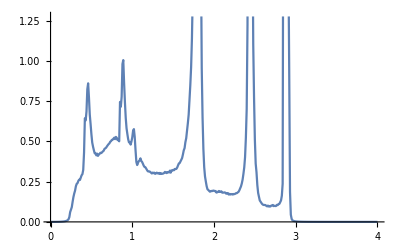

```mathematica
ListPlot[%143,Joined->True]
```

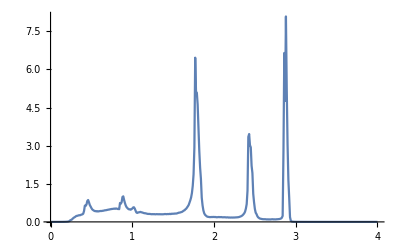

```mathematica
ListPlot[%143,Joined->True,PlotRange->All]
```

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.0001,1,0,0.9],5000]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000489775},{0.01,0.000376198},{0.02,0.000286297},{0.03,0.000250898},{0.04,0.000232117},{0.05,0.000259657},{0.06,0.000313945},{0.07,0.000406479},{0.08,0.000512223},{0.09,0.000667976},{0.1,0.000860209},{0.11,0.00110964},{0.12,0.00143061},{0.13,0.00181177},{0.14,0.00222073},{0.15,0.00288467},{0.16,0.00357287},{0.17,0.00461844},{0.18,0.00600371},{0.19,0.00773265},{0.2,0.0102016},{0.21,0.014152},{0.22,0.0203657},{0.23,0.0352949},{0.24,0.0730207},{0.25,0.0850252},{0.26,0.107551},{0.27,0.130069},{0.28,0.160849},{0.29,0.175994},{0.3,0.180094},{0.31,0.184314},{0.32,0.191854},{0.33,0.200424},{0.34,0.204346},{0.35,0.213991},{0.36,0.218482},{0.37,0.232664},{0.38,0.256842},{0.39,0.294503},{0.4,0.358138},{0.41,0.529507},{0.42,0.754065},{0.43,0.69389},{0.44,0.74909},{0.45,0.762558},{0.46,0.84555},{0.47,0.824701},{0.48,0.755638},{0.49,0.661849},{0.5,0.606286},{0.51,0.556588},{0.52,0.503702},{0.53,0.473534},{0.54,0.448854},{0.55,0.422422},{0.56,0.394687},{0.57,0.3818},{0.58,0.366105},{0.59,0.360589},{0.6,0.351817},{0.61,0.340651},{0.62,0.343588},{0.63,0.338846},{0.64,0.336106},{0.65,0.337805},{0.66,0.328371},{0.67,0.334518},{0.68,0.330024},{0.69,0.333864},{0.7,0.32857},{0.71,0.344382},{0.72,0.342582},{0.73,0.341889},{0.74,0.349352},{0.75,0.349406},{0.76,0.345268},{0.77,0.352034},{0.78,0.360972},{0.79,0.364287},{0.8,0.373245},{0.81,0.367676},{0.82,0.383746},{0.83,0.413091},{0.84,0.500888},{0.85,0.914262},{0.86,0.862052},{0.87,0.848261},{0.88,0.982825},{0.89,1.05611},{0.9,0.993165},{0.91,0.889624},{0.92,0.781622},{0.93,0.710188},{0.94,0.646706},{0.95,0.591353},{0.96,0.549424},{0.97,0.507592},{0.98,0.491621},{0.99,0.466788},{1.,0.445966},{1.01,0.435132},{1.02,0.432193},{1.03,0.418076},{1.04,0.402637},{1.05,0.382388},{1.06,0.368068},{1.07,0.367195},{1.08,0.372945},{1.09,0.377049},{1.1,0.391012},{1.11,0.393812},{1.12,0.402779},{1.13,0.397154},{1.14,0.390389},{1.15,0.377008},{1.16,0.367976},{1.17,0.364245},{1.18,0.355259},{1.19,0.349224},{1.2,0.34592},{1.21,0.345987},{1.22,0.336852},{1.23,0.337442},{1.24,0.331334},{1.25,0.321725},{1.26,0.318057},{1.27,0.311839},{1.28,0.31559},{1.29,0.312802},{1.3,0.308201},{1.31,0.313155},{1.32,0.307976},{1.33,0.303257},{1.34,0.305813},{1.35,0.301604},{1.36,0.299784},{1.37,0.305113},{1.38,0.306229},{1.39,0.308868},{1.4,0.309884},{1.41,0.304545},{1.42,0.309831},{1.43,0.313275},{1.44,0.319226},{1.45,0.313686},{1.46,0.326538},{1.47,0.326884},{1.48,0.329931},{1.49,0.332003},{1.5,0.340305},{1.51,0.347622},{1.52,0.353941},{1.53,0.359166},{1.54,0.366462},{1.55,0.379645},{1.56,0.386215},{1.57,0.399188},{1.58,0.407716},{1.59,0.433279},{1.6,0.439354},{1.61,0.455623},{1.62,0.480216},{1.63,0.502807},{1.64,0.522807},{1.65,0.560595},{1.66,0.590296},{1.67,0.639179},{1.68,0.692584},{1.69,0.758864},{1.7,0.836286},{1.71,0.930896},{1.72,1.06121},{1.73,1.24989},{1.74,1.51433},{1.75,1.93778},{1.76,2.95818},{1.77,5.72606},{1.78,4.18021},{1.79,3.5917},{1.8,3.66945},{1.81,3.47869},{1.82,3.26747},{1.83,3.06102},{1.84,2.53381},{1.85,2.02255},{1.86,1.65044},{1.87,1.23827},{1.88,1.04629},{1.89,0.749254},{1.9,0.540493},{1.91,0.455325},{1.92,0.36617},{1.93,0.319088},{1.94,0.283488},{1.95,0.249025},{1.96,0.22558},{1.97,0.204303},{1.98,0.193519},{1.99,0.185579},{2.,0.174353},{2.01,0.161668},{2.02,0.159468},{2.03,0.154312},{2.04,0.149019},{2.05,0.141974},{2.06,0.144972},{2.07,0.140327},{2.08,0.13581},{2.09,0.132517},{2.1,0.135015},{2.11,0.128086},{2.12,0.130243},{2.13,0.132341},{2.14,0.130331},{2.15,0.132863},{2.16,0.132917},{2.17,0.134104},{2.18,0.131923},{2.19,0.132389},{2.2,0.133824},{2.21,0.135309},{2.22,0.133968},{2.23,0.140625},{2.24,0.142367},{2.25,0.150044},{2.26,0.152686},{2.27,0.161777},{2.28,0.167869},{2.29,0.171909},{2.3,0.183399},{2.31,0.189747},{2.32,0.212832},{2.33,0.227296},{2.34,0.25319},{2.35,0.278727},{2.36,0.316568},{2.37,0.367424},{2.38,0.43493},{2.39,0.532408},{2.4,0.713192},{2.41,1.23059},{2.42,2.96684},{2.43,3.07412},{2.44,2.91912},{2.45,3.15206},{2.46,3.10709},{2.47,2.68559},{2.48,2.43928},{2.49,1.9663},{2.5,1.62557},{2.51,0.920076},{2.52,0.815671},{2.53,0.564596},{2.54,0.452664},{2.55,0.362172},{2.56,0.325907},{2.57,0.273639},{2.58,0.253828},{2.59,0.223318},{2.6,0.1997},{2.61,0.184359},{2.62,0.163405},{2.63,0.147091},{2.64,0.149928},{2.65,0.134617},{2.66,0.126236},{2.67,0.122191},{2.68,0.129787},{2.69,0.119081},{2.7,0.113141},{2.71,0.123008},{2.72,0.120876},{2.73,0.114868},{2.74,0.120884},{2.75,0.122816},{2.76,0.124041},{2.77,0.128411},{2.78,0.136434},{2.79,0.138673},{2.8,0.153813},{2.81,0.161276},{2.82,0.201648},{2.83,0.229591},{2.84,0.402922},{2.85,4.20777},{2.86,10.814},{2.87,17.6655},{2.88,19.5761},{2.89,14.1587},{2.9,15.1818},{2.91,13.5193},{2.92,6.34343},{2.93,11.4216},{2.94,8.95313},{2.95,7.1583},{2.96,2.87885},{2.97,0.219866},{2.98,0.11229},{2.99,0.0485615},{3.,0.0124345},{3.01,0.00928343},{3.02,0.00726415},{3.03,0.00800515},{3.04,0.00510523},{3.05,0.00399921},{3.06,0.00340608},{3.07,0.00295786},{3.08,0.00260697},{3.09,0.00218419},{3.1,0.00174107},{3.11,0.00165556},{3.12,0.00147977},{3.13,0.00127158},{3.14,0.00114566},{3.15,0.000988899},{3.16,0.000873846},{3.17,0.000796304},{3.18,0.000734679},{3.19,0.000647983},{3.2,0.000590651},{3.21,0.000541423},{3.22,0.000489144},{3.23,0.000442261},{3.24,0.000391735},{3.25,0.000361977},{3.26,0.000328295},{3.27,0.000310368},{3.28,0.000283371},{3.29,0.000261634},{3.3,0.000242009},{3.31,0.000226179},{3.32,0.000212876},{3.33,0.000194636},{3.34,0.000176346},{3.35,0.000160746},{3.36,0.000155171},{3.37,0.000142883},{3.38,0.000129042},{3.39,0.000123442},{3.4,0.000116483},{3.41,0.000113828},{3.42,0.000103537},{3.43,0.0000950418},{3.44,0.0000862906},{3.45,0.0000857216},{3.46,0.0000772433},{3.47,0.0000711641},{3.48,0.0000714859},{3.49,0.0000679255},{3.5,0.0000643003},{3.51,0.0000532368},{3.52,0.0000541234},{3.53,0.0000498763},{3.54,0.0000491976},{3.55,0.0000431526},{3.56,0.000043938},{3.57,0.0000392757},{3.58,0.0000369099},{3.59,0.0000376539},{3.6,0.0000340973},{3.61,0.0000312061},{3.62,0.0000295634},{3.63,0.000029005},{3.64,0.0000277171},{3.65,0.0000257149},{3.66,0.0000249382},{3.67,0.0000239043},{3.68,0.0000226012},{3.69,0.0000206627},{3.7,0.0000199743},{3.71,0.0000191531},{3.72,0.0000183062},{3.73,0.0000181401},{3.74,0.0000170075},{3.75,0.0000163416},{3.76,0.0000157138},{3.77,0.0000138808},{3.78,0.0000135398},{3.79,0.0000130244},{3.8,0.0000122551},{3.81,0.000011178},{3.82,0.0000111112},{3.83,0.0000112587},{3.84,0.0000101379},{3.85,9.65426×10^-6},{3.86,9.33434×10^-6},{3.87,9.29354×10^-6},{3.88,8.77277×10^-6},{3.89,8.51883×10^-6},{3.9,7.73965×10^-6},{3.91,7.48088×10^-6},{3.92,7.63447×10^-6},{3.93,7.12252×10^-6},{3.94,6.81567×10^-6},{3.95,6.00768×10^-6},{3.96,6.15332×10^-6},{3.97,6.07974×10^-6},{3.98,5.79148×10^-6},{3.99,5.7552×10^-6},{4.,5.32292×10^-6}}

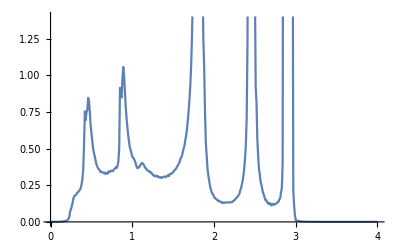

```mathematica
ListPlot[%144,Joined->True]
```

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.0001,1,0,0.3],5000]]},{ω,Range[0,4,0.01]}]
```

{{0.,5.05173×10^-6},{0.01,2.80533×10^-6},{0.02,3.82072×10^-6},{0.03,8.00242×10^-6},{0.04,0.0000155773},{0.05,0.0000261681},{0.06,0.000041982},{0.07,0.0000615165},{0.08,0.0000845053},{0.09,0.000116641},{0.1,0.000153547},{0.11,0.000201713},{0.12,0.000265755},{0.13,0.000343092},{0.14,0.000431451},{0.15,0.00055916},{0.16,0.000720391},{0.17,0.000936278},{0.18,0.00124994},{0.19,0.00174336},{0.2,0.00243597},{0.21,0.00369048},{0.22,0.00618006},{0.23,0.0129688},{0.24,0.0344898},{0.25,0.0458038},{0.26,0.341055},{0.27,0.51511},{0.28,0.59532},{0.29,0.628334},{0.3,0.650143},{0.31,0.661664},{0.32,0.671556},{0.33,0.683843},{0.34,0.688551},{0.35,0.693866},{0.36,0.692541},{0.37,0.691782},{0.38,0.686726},{0.39,0.680795},{0.4,0.661137},{0.41,0.588618},{0.42,0.527448},{0.43,0.617554},{0.44,0.834607},{0.45,0.705638},{0.46,0.735956},{0.47,0.76982},{0.48,0.830705},{0.49,0.877929},{0.5,0.923155},{0.51,0.978391},{0.52,1.02233},{0.53,1.05297},{0.54,1.08022},{0.55,1.10851},{0.56,1.13984},{0.57,1.15011},{0.58,1.16668},{0.59,1.19432},{0.6,1.21661},{0.61,1.21864},{0.62,1.23727},{0.63,1.24795},{0.64,1.25649},{0.65,1.26952},{0.66,1.27374},{0.67,1.27791},{0.68,1.29199},{0.69,1.29644},{0.7,1.30647},{0.71,1.31131},{0.72,1.32027},{0.73,1.32204},{0.74,1.33235},{0.75,1.33074},{0.76,1.34707},{0.77,1.34067},{0.78,1.35238},{0.79,1.35055},{0.8,1.35445},{0.81,1.35425},{0.82,1.35309},{0.83,1.33513},{0.84,1.27236},{0.85,0.967882},{0.86,0.849739},{0.87,0.908369},{0.88,0.775642},{0.89,0.819178},{0.9,0.929769},{0.91,1.03054},{0.92,1.15547},{0.93,1.24484},{0.94,1.34243},{0.95,1.42571},{0.96,1.51515},{0.97,1.58513},{0.98,1.6793},{0.99,1.75767},{1.,1.81987},{1.01,1.85489},{1.02,1.39178},{1.03,0.490763},{1.04,0.332073},{1.05,0.360413},{1.06,0.479693},{1.07,0.646978},{1.08,0.796213},{1.09,0.915685},{1.1,0.98595},{1.11,1.05878},{1.12,1.10987},{1.13,1.14757},{1.14,1.18772},{1.15,1.22458},{1.16,1.24453},{1.17,1.26791},{1.18,1.28406},{1.19,1.29767},{1.2,1.32097},{1.21,1.32306},{1.22,1.32841},{1.23,1.33345},{1.24,1.33296},{1.25,1.34224},{1.26,1.34242},{1.27,1.34035},{1.28,1.31805},{1.29,1.34822},{1.3,1.34157},{1.31,1.34925},{1.32,1.35453},{1.33,1.35285},{1.34,1.3367},{1.35,1.33363},{1.36,1.33594},{1.37,1.32983},{1.38,1.32767},{1.39,1.31357},{1.4,1.31237},{1.41,1.30856},{1.42,1.28991},{1.43,1.28542},{1.44,1.26493},{1.45,1.26589},{1.46,1.25589},{1.47,1.2311},{1.48,1.24055},{1.49,1.22705},{1.5,1.20661},{1.51,1.19092},{1.52,1.16805},{1.53,1.16703},{1.54,1.12936},{1.55,1.10791},{1.56,1.08918},{1.57,1.07558},{1.58,1.06603},{1.59,1.03313},{1.6,0.988874},{1.61,0.959849},{1.62,0.950006},{1.63,0.898954},{1.64,0.861445},{1.65,0.834118},{1.66,0.793473},{1.67,0.746253},{1.68,0.704448},{1.69,0.668064},{1.7,0.627766},{1.71,0.600487},{1.72,0.594559},{1.73,0.633893},{1.74,0.763012},{1.75,1.11891},{1.76,2.21995},{1.77,8.09704},{1.78,5.22662},{1.79,2.41984},{1.8,0.623719},{1.81,0.797562},{1.82,0.946778},{1.83,1.01392},{1.84,1.05284},{1.85,1.07422},{1.86,1.08248},{1.87,1.09943},{1.88,1.10752},{1.89,1.11102},{1.9,1.11829},{1.91,1.12218},{1.92,1.12479},{1.93,1.12778},{1.94,1.11544},{1.95,1.12205},{1.96,1.11019},{1.97,1.1111},{1.98,1.10535},{1.99,1.09933},{2.,1.09476},{2.01,1.09199},{2.02,1.092},{2.03,1.08775},{2.04,1.07912},{2.05,1.08175},{2.06,1.0608},{2.07,1.07181},{2.08,1.04933},{2.09,1.0446},{2.1,1.03948},{2.11,1.02586},{2.12,1.03146},{2.13,1.01154},{2.14,1.00476},{2.15,1.00278},{2.16,0.989349},{2.17,0.981317},{2.18,0.965894},{2.19,0.950353},{2.2,0.945626},{2.21,0.926072},{2.22,0.92162},{2.23,0.896599},{2.24,0.883423},{2.25,0.869968},{2.26,0.869374},{2.27,0.83787},{2.28,0.817531},{2.29,0.792415},{2.3,0.77213},{2.31,0.744318},{2.32,0.717339},{2.33,0.682526},{2.34,0.657392},{2.35,0.611773},{2.36,0.582065},{2.37,0.542407},{2.38,0.507314},{2.39,0.489797},{2.4,0.549376},{2.41,0.99683},{2.42,3.06537},{2.43,2.60665},{2.44,1.04526},{2.45,0.350887},{2.46,0.458548},{2.47,0.520504},{2.48,0.544561},{2.49,0.552634},{2.5,0.566387},{2.51,0.570732},{2.52,0.578941},{2.53,0.579597},{2.54,0.575863},{2.55,0.575767},{2.56,0.573103},{2.57,0.574341},{2.58,0.57379},{2.59,0.57028},{2.6,0.569147},{2.61,0.564703},{2.62,0.569372},{2.63,0.561632},{2.64,0.563384},{2.65,0.555185},{2.66,0.55401},{2.67,0.545186},{2.68,0.554564},{2.69,0.5336},{2.7,0.536816},{2.71,0.523699},{2.72,0.516757},{2.73,0.512119},{2.74,0.507013},{2.75,0.490714},{2.76,0.47395},{2.77,0.465789},{2.78,0.460819},{2.79,0.439506},{2.8,0.422522},{2.81,0.400306},{2.82,0.371148},{2.83,0.324465},{2.84,0.264223},{2.85,0.369868},{2.86,0.321041},{2.87,0.17969},{2.88,0.0119946},{2.89,0.00409349},{2.9,0.00229489},{2.91,0.00157615},{2.92,0.00118785},{2.93,0.000891426},{2.94,0.000707341},{2.95,0.00055845},{2.96,0.000446317},{2.97,0.000389395},{2.98,0.000316294},{2.99,0.00027643},{3.,0.00023391},{3.01,0.000185308},{3.02,0.000172956},{3.03,0.000149793},{3.04,0.000137203},{3.05,0.000120253},{3.06,0.000101093},{3.07,0.0000890848},{3.08,0.0000768343},{3.09,0.0000699372},{3.1,0.0000669858},{3.11,0.000058564},{3.12,0.0000528042},{3.13,0.0000465836},{3.14,0.0000418898},{3.15,0.0000399922},{3.16,0.0000362705},{3.17,0.000033441},{3.18,0.0000293707},{3.19,0.0000290235},{3.2,0.0000258647},{3.21,0.0000255072},{3.22,0.0000223786},{3.23,0.0000204149},{3.24,0.0000180324},{3.25,0.0000158897},{3.26,0.000015923},{3.27,0.0000150742},{3.28,0.0000135814},{3.29,0.0000129135},{3.3,0.0000117774},{3.31,0.0000112393},{3.32,0.0000100763},{3.33,9.68251×10^-6},{3.34,9.14052×10^-6},{3.35,8.32018×10^-6},{3.36,8.16569×10^-6},{3.37,7.08563×10^-6},{3.38,6.93924×10^-6},{3.39,6.40874×10^-6},{3.4,6.12791×10^-6},{3.41,5.89005×10^-6},{3.42,5.46565×10^-6},{3.43,5.21636×10^-6},{3.44,4.84627×10^-6},{3.45,4.98715×10^-6},{3.46,4.48204×10^-6},{3.47,3.96499×10^-6},{3.48,3.8303×10^-6},{3.49,3.75583×10^-6},{3.5,3.48843×10^-6},{3.51,3.16441×10^-6},{3.52,3.05707×10^-6},{3.53,3.01706×10^-6},{3.54,2.85323×10^-6},{3.55,2.6845×10^-6},{3.56,2.56811×10^-6},{3.57,2.38516×10^-6},{3.58,2.27401×10^-6},{3.59,2.12239×10^-6},{3.6,2.12021×10^-6},{3.61,1.84181×10^-6},{3.62,1.86318×10^-6},{3.63,1.76912×10^-6},{3.64,1.68768×10^-6},{3.65,1.59837×10^-6},{3.66,1.474×10^-6},{3.67,1.4096×10^-6},{3.68,1.29634×10^-6},{3.69,1.29228×10^-6},{3.7,1.22549×10^-6},{3.71,1.2015×10^-6},{3.72,1.13768×10^-6},{3.73,1.06624×10^-6},{3.74,1.00884×10^-6},{3.75,1.01262×10^-6},{3.76,9.57734×10^-7},{3.77,9.31984×10^-7},{3.78,8.70954×10^-7},{3.79,8.4427×10^-7},{3.8,8.15148×10^-7},{3.81,7.32857×10^-7},{3.82,7.16607×10^-7},{3.83,7.07955×10^-7},{3.84,6.78403×10^-7},{3.85,6.52221×10^-7},{3.86,6.27139×10^-7},{3.87,6.13096×10^-7},{3.88,5.69053×10^-7},{3.89,5.83864×10^-7},{3.9,5.56915×10^-7},{3.91,5.33021×10^-7},{3.92,4.94638×10^-7},{3.93,4.75846×10^-7},{3.94,4.48922×10^-7},{3.95,4.35304×10^-7},{3.96,4.15814×10^-7},{3.97,4.01057×10^-7},{3.98,3.71897×10^-7},{3.99,3.57992×10^-7},{4.,3.60207×10^-7}}

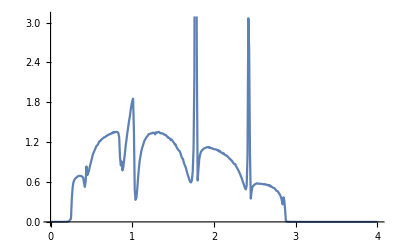

```mathematica
ListPlot[%145,Joined->True]
```

```mathematica
Table[{ω,Mean[Table[tr1[ω,0.0001,1,0,1],5000]]},{ω,Range[0,4,0.01]}]
```

{{0.,0.000817074},{0.01,0.000625472},{0.02,0.000458336},{0.03,0.000399613},{0.04,0.000386561},{0.05,0.000365752},{0.06,0.000409224},{0.07,0.000525264},{0.08,0.000623868},{0.09,0.000787592},{0.1,0.00103004},{0.11,0.00130629},{0.12,0.00167222},{0.13,0.0020496},{0.14,0.00262205},{0.15,0.00331126},{0.16,0.00416971},{0.17,0.00512551},{0.18,0.00669409},{0.19,0.00880879},{0.2,0.0115864},{0.21,0.0156257},{0.22,0.0235841},{0.23,0.0377864},{0.24,0.0762538},{0.25,0.0882116},{0.26,0.109156},{0.27,0.134259},{0.28,0.168143},{0.29,0.196072},{0.3,0.195938},{0.31,0.195659},{0.32,0.202303},{0.33,0.20163},{0.34,0.20311},{0.35,0.20994},{0.36,0.223236},{0.37,0.25053},{0.38,0.273717},{0.39,0.313327},{0.4,0.388042},{0.41,0.577587},{0.42,0.842381},{0.43,0.776735},{0.44,0.760258},{0.45,0.804428},{0.46,0.843124},{0.47,0.819245},{0.48,0.758083},{0.49,0.697768},{0.5,0.646523},{0.51,0.575303},{0.52,0.530282},{0.53,0.479889},{0.54,0.459712},{0.55,0.420211},{0.56,0.410415},{0.57,0.385146},{0.58,0.367799},{0.59,0.35796},{0.6,0.345078},{0.61,0.337765},{0.62,0.323597},{0.63,0.319576},{0.64,0.30842},{0.65,0.309362},{0.66,0.311225},{0.67,0.30443},{0.68,0.304583},{0.69,0.309484},{0.7,0.312726},{0.71,0.301905},{0.72,0.302414},{0.73,0.304491},{0.74,0.311161},{0.75,0.317407},{0.76,0.318399},{0.77,0.320968},{0.78,0.324471},{0.79,0.335159},{0.8,0.341301},{0.81,0.352189},{0.82,0.370017},{0.83,0.419781},{0.84,0.526266},{0.85,1.00263},{0.86,0.887523},{0.87,0.883064},{0.88,0.996471},{0.89,1.05148},{0.9,1.04236},{0.91,0.936352},{0.92,0.826918},{0.93,0.739686},{0.94,0.676456},{0.95,0.635039},{0.96,0.585938},{0.97,0.555009},{0.98,0.519365},{0.99,0.503008},{1.,0.468542},{1.01,0.440158},{1.02,0.420525},{1.03,0.410918},{1.04,0.40334},{1.05,0.386915},{1.06,0.376813},{1.07,0.374821},{1.08,0.384659},{1.09,0.372539},{1.1,0.390758},{1.11,0.391768},{1.12,0.380969},{1.13,0.400177},{1.14,0.386873},{1.15,0.391746},{1.16,0.385225},{1.17,0.378711},{1.18,0.368726},{1.19,0.357334},{1.2,0.360119},{1.21,0.355996},{1.22,0.354637},{1.23,0.343603},{1.24,0.339273},{1.25,0.336172},{1.26,0.33449},{1.27,0.3296},{1.28,0.331289},{1.29,0.329708},{1.3,0.323401},{1.31,0.316904},{1.32,0.316271},{1.33,0.319616},{1.34,0.31804},{1.35,0.312524},{1.36,0.307395},{1.37,0.313706},{1.38,0.314876},{1.39,0.314771},{1.4,0.319886},{1.41,0.322944},{1.42,0.317817},{1.43,0.320387},{1.44,0.331705},{1.45,0.330888},{1.46,0.340368},{1.47,0.344271},{1.48,0.339706},{1.49,0.348149},{1.5,0.35292},{1.51,0.364215},{1.52,0.375669},{1.53,0.373392},{1.54,0.38299},{1.55,0.392641},{1.56,0.402584},{1.57,0.420125},{1.58,0.439898},{1.59,0.44348},{1.6,0.457408},{1.61,0.474314},{1.62,0.507032},{1.63,0.526541},{1.64,0.556786},{1.65,0.588155},{1.66,0.614967},{1.67,0.672182},{1.68,0.717052},{1.69,0.762945},{1.7,0.850962},{1.71,0.965847},{1.72,1.06577},{1.73,1.27859},{1.74,1.55109},{1.75,1.93398},{1.76,2.95737},{1.77,5.49389},{1.78,4.0563},{1.79,3.43145},{1.8,3.40008},{1.81,3.21575},{1.82,2.8584},{1.83,2.89716},{1.84,2.37053},{1.85,2.12246},{1.86,1.94393},{1.87,1.59068},{1.88,1.31606},{1.89,1.05344},{1.9,0.938673},{1.91,0.695517},{1.92,0.526243},{1.93,0.440074},{1.94,0.374009},{1.95,0.343314},{1.96,0.304204},{1.97,0.275918},{1.98,0.231663},{1.99,0.223277},{2.,0.210755},{2.01,0.198481},{2.02,0.188748},{2.03,0.176274},{2.04,0.172313},{2.05,0.160895},{2.06,0.153653},{2.07,0.147669},{2.08,0.149141},{2.09,0.140188},{2.1,0.141353},{2.11,0.134571},{2.12,0.137388},{2.13,0.138363},{2.14,0.135475},{2.15,0.13616},{2.16,0.138788},{2.17,0.137297},{2.18,0.135429},{2.19,0.137921},{2.2,0.140298},{2.21,0.142123},{2.22,0.140042},{2.23,0.143531},{2.24,0.146008},{2.25,0.151636},{2.26,0.155208},{2.27,0.163342},{2.28,0.171251},{2.29,0.183422},{2.3,0.187158},{2.31,0.206135},{2.32,0.21998},{2.33,0.238788},{2.34,0.260448},{2.35,0.28409},{2.36,0.327617},{2.37,0.374947},{2.38,0.450404},{2.39,0.548704},{2.4,0.722533},{2.41,1.21631},{2.42,2.57448},{2.43,3.31426},{2.44,2.94875},{2.45,3.05127},{2.46,2.40157},{2.47,2.48818},{2.48,2.38582},{2.49,2.23435},{2.5,1.43574},{2.51,1.35429},{2.52,1.36894},{2.53,0.816255},{2.54,0.678064},{2.55,0.497576},{2.56,0.437257},{2.57,0.375845},{2.58,0.324677},{2.59,0.291276},{2.6,0.279058},{2.61,0.249169},{2.62,0.235258},{2.63,0.236907},{2.64,0.204227},{2.65,0.189484},{2.66,0.174919},{2.67,0.171459},{2.68,0.169966},{2.69,0.161705},{2.7,0.167182},{2.71,0.152047},{2.72,0.151284},{2.73,0.159675},{2.74,0.146982},{2.75,0.158608},{2.76,0.157011},{2.77,0.162767},{2.78,0.173067},{2.79,0.183268},{2.8,0.196072},{2.81,0.202991},{2.82,0.247248},{2.83,0.2941},{2.84,0.443675},{2.85,3.10773},{2.86,13.0547},{2.87,30.1904},{2.88,36.9627},{2.89,48.7063},{2.9,19.1683},{2.91,18.322},{2.92,21.0086},{2.93,19.9056},{2.94,6.44831},{2.95,11.0312},{2.96,9.82831},{2.97,0.996188},{2.98,1.05991},{2.99,0.289373},{3.,0.30678},{3.01,0.156532},{3.02,0.0461051},{3.03,0.0129156},{3.04,0.0091008},{3.05,0.00716485},{3.06,0.00579552},{3.07,0.00521575},{3.08,0.00443766},{3.09,0.00353499},{3.1,0.00307346},{3.11,0.00265396},{3.12,0.00236583},{3.13,0.00213118},{3.14,0.00184521},{3.15,0.00161186},{3.16,0.00137693},{3.17,0.00126322},{3.18,0.00111103},{3.19,0.000972507},{3.2,0.000934908},{3.21,0.000812622},{3.22,0.000730129},{3.23,0.000665566},{3.24,0.000616313},{3.25,0.000558036},{3.26,0.000500147},{3.27,0.000484974},{3.28,0.00043022},{3.29,0.000401125},{3.3,0.000353721},{3.31,0.0003287},{3.32,0.00031173},{3.33,0.000279909},{3.34,0.000250295},{3.35,0.000242544},{3.36,0.000220244},{3.37,0.000206714},{3.38,0.000203531},{3.39,0.000177503},{3.4,0.000171558},{3.41,0.000161367},{3.42,0.00014217},{3.43,0.000135391},{3.44,0.000133964},{3.45,0.000123348},{3.46,0.000112638},{3.47,0.000104506},{3.48,0.0000994495},{3.49,0.0000911424},{3.5,0.000088811},{3.51,0.0000806481},{3.52,0.0000749164},{3.53,0.0000727905},{3.54,0.0000655794},{3.55,0.0000643159},{3.56,0.0000613579},{3.57,0.0000584395},{3.58,0.0000547476},{3.59,0.0000475906},{3.6,0.0000456291},{3.61,0.0000460391},{3.62,0.0000424208},{3.63,0.0000400351},{3.64,0.0000381169},{3.65,0.0000334637},{3.66,0.0000341289},{3.67,0.0000323422},{3.68,0.0000303158},{3.69,0.0000300857},{3.7,0.0000275943},{3.71,0.0000254367},{3.72,0.000025919},{3.73,0.0000243801},{3.74,0.0000227663},{3.75,0.0000217256},{3.76,0.0000215294},{3.77,0.0000197575},{3.78,0.0000188989},{3.79,0.0000177795},{3.8,0.0000168542},{3.81,0.0000154014},{3.82,0.000016117},{3.83,0.0000149893},{3.84,0.0000139304},{3.85,0.0000137163},{3.86,0.0000126649},{3.87,0.0000127017},{3.88,0.0000112748},{3.89,0.0000113691},{3.9,0.0000104153},{3.91,0.0000103003},{3.92,9.63106×10^-6},{3.93,9.30303×10^-6},{3.94,9.25767×10^-6},{3.95,8.78958×10^-6},{3.96,8.42327×10^-6},{3.97,8.00659×10^-6},{3.98,7.51988×10^-6},{3.99,7.27315×10^-6},{4.,7.05429×10^-6}}

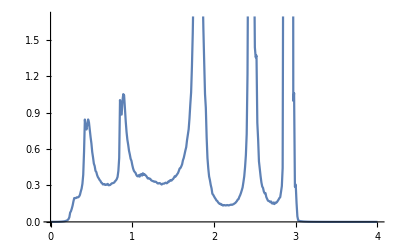

```mathematica
ListPlot[%146,Joined->True]
```